# What Is Quantum Computation?

Welcome to the first lesson of this course! We’ll start by briefly revisiting classical computation through clear, hands-on examples. Then, we’ll shift our focus to the quantum realm, where you’ll explore a few foundational quantum circuits. Each example will come with accompanying code; don’t worry if it doesn’t all make sense right away. As we progress, you’ll gradually build both your understanding of quantum concepts and your coding skills.

## Key Concepts

Quantum Circuit

Qubit

Measurement

## Classical Computation

In order to understand quantum computation, it helps to compare it to classical computation. To compute something, you have to be able to use rules to determine what should be the output from a list of inputs. You can think of computing as starting with the inputs and following the rules to reach an output.

Consider two binary numbers “01” and “10” and let’s see how we can add them. First, each bit-string is interpreted as a base-2 number rather than ordinary decimal, so “01” becomes one and “10” becomes two.

Define binary strings:

```mathematica
a="01";b="10";
```

Construct the number from the base-2 digits of a:

```mathematica
FromDigits[a,2]
```

1

Construct the number from the base-2 digits of b:

```mathematica
FromDigits[b,2]
```

2

Add the numbers using normal addition:

```mathematica
FromDigits[a,2]+FromDigits[b,2]
```

3

Convert the total back into bit-string:

```mathematica
IntegerString[FromDigits[a,2]+FromDigits[b,2],2]
```

11

Let’s consider another example. Add two binary strings 100 and 011:

```mathematica
a="101";
b="011";
IntegerString[FromDigits[a,2]+FromDigits[b,2],2]
```

1000

Now something interesting happened in above calculation. Pay attention to the string length of initial numbers and final total. The original bit-strings had the string length of 3 while the final answer is a four-bit string. Let’s dive in a bit more.

What are all the states of a sequence of three classical bits?

```mathematica
threeBits=Tuples[{0,1},3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

What are the corresponding numbers from above base-2 digits?

```mathematica
FromDigits[#,2]&/@threeBits
```

{0,1,2,3,4,5,6,7}

With a 3-bit string you can represent 0–7; in general, n bits represent 0 to 2^n-1. Returning to the example, adding 101 and 011 gives 8, which exceeds the 3-bit range. This means in-place addition is modulo 2^n, so the sum wraps to 000 unless you provide an extra bit to capture the carry.

```mathematica
FromDigits[a,2]+FromDigits[b,2]
```

8

To encode that result as a bitstring, we need at least 4 bits (since 8 requires 4-bit representation).

```mathematica
IntegerString[FromDigits[a,2]+FromDigits[b,2],2]
```

1000

If you insist on staying within 3 bits, perform all operations modulo 8 (wrap-around arithmetic).

```mathematica
Mod[FromDigits[a,2]+FromDigits[b,2],2^3]
```

0

Then the 3-bit string of the above result is:

```mathematica
IntegerString[0,2,3]
```

000

It is also possible to encode information in such sequences of classical bits to represent problems of interest. For example, each of those bit sequences could also encode letter characters with a different encoding scheme:

```mathematica
FromLetterNumber[FromDigits[#,2]]&/@threeBits
```

{ ,a,b,c,d,e,f,g}

With yet another encoding scheme, those same bit sequences could represent colors with opacity:

```mathematica
Apply[RGBColor,#]&/@threeBits
```

{RGBColor[0, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 1, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 1],RGBColor[1, 1, 0],RGBColor[1, 1, 1]}

Having seen how a 3-bit register cleanly enumerates eight distinct states and how different encodings map those states to numbers, letters, or colors, we now move to the quantum setting. There the same eight basis strings exist, but a 3-qubit register can also occupy complex superpositions of them, and even entangled combinations that have no classical analogue. The rules for storing and extracting information therefore change: measurement reveals a single basis outcome, while computation exploits interference among amplitudes.

## Quantum Circuits and Qubits

Now we’ll dive directly into quantum computation. We’ll introduce common terms and concepts widely used in quantum information. Some details will be only briefly mentioned. For each topic, we’ll highlight what to focus on for a first exposure, and later we’ll return to expand on each concept in more depth.

The diagram below represents an example of a quantum circuit:

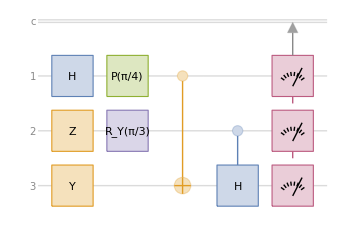

```mathematica
qc=QuantumCircuitOperator[{"H","Z"->2,"Y"->3,"P"[π/4],"CNOT"->{1,3},"RY"[π/3]->2,"CH"->{2,3},Range[3]}];
qc["Diagram"]
```

Notice how the circuit diagram has several wires, labeled c, 1, 2 and 3. Wires 1, 2 and 3 represent qubits (quantum bits) instead of classical bits. This is a 3-qubit system, meaning that the state can be described in the complex vector space ℂ^8. The previous eight classical bits can form a convenient basis (usually called as the computational basis). Those 3-bits in quantum are represented by wrapping them around a notation … which is called a ket. In general, a ket is a shorthand representation of a complex-valued vector. A general 3-qubit state is a complex linear combination of those eight basis states.

```mathematica
TraditionalForm[#]->MatrixForm[#["StateVector"]]&/@QuantumBasis[2,3]["BasisStates"]
```

{000→(1
0
0
0
0
0
0
0),001→(0
1
0
0
0
0
0
0),010→(0
0
1
0
0
0
0
0),011→(0
0
0
1
0
0
0
0),100→(0
0
0
0
1
0
0
0),101→(0
0
0
0
0
1
0
0),110→(0
0
0
0
0
0
1
0),111→(0
0
0
0
0
0
0
1)}

A quantum circuit is read from left to right. For example, the first operation—represented by the blue box labeled H, acts only on the first wire, while some operations act on more than one wire; they are multi-qubit gates. The boxes that look like gauges on the right hand side of the diagram represent measurement and point to the wire labeled c. The wire labeled c represents a classical system (such as part of a regular computer) where the results of the measurements on qubits are stored.  All operations shown except for measurements are unitary and reversible, a key feature we’ll explore in more detail later. You can think of each box as performing a transformation on the quantum state of one or more wires. These transformations must obey fundamental principles dictated by quantum theory.

What are the results of running this circuit? Since measurements are included at the end, executing the circuit returns a quantum measurement object in the Wolfram Quantum Framework. This object contains the probability distribution over possible bitstrings and can be sampled to generate measurement outcomes:

```mathematica
measurements=qc[]
```

QuantumMeasurement[…]

Note that by executing the code above, we performed a quantum computation—but it was carried out on a classical computer (your PC). This is exactly what a quantum simulator does: it mimics quantum behavior and performs computations using the rules of quantum mechanics, all within classical hardware.

What are the results of the measurement in this circuit?

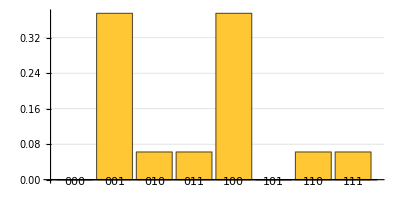

```mathematica
measurements["ProbabilitiesPlot",]
```

Notice that the possible outcomes of a quantum measurement are simply classical bit sequences. In the earlier classical computation examples, the rules were deterministic: each input led to a definite output. In contrast, quantum computation typically yields a range of possible outcomes, each with a certain probability. This is because quantum theory provides a probabilistic description of measurement results, with the distribution determined by the state just before measurement (and the chosen measurement basis).

For a quantum program to be useful, you want to arrange things so that the probability of measuring a result that encodes a desired solution to your problem is high.

Additionally, you can track how the quantum state evolves as gates are applied. Although we have not yet discussed the state in full detail, for now focus on the linear combination of computational-basis bitstrings and examine the coefficient (amplitude) of each term. These amplitudes update linearly under gates, and their squared magnitudes determine the probabilities of the corresponding bitstrings upon measurement.

```mathematica
Grid[Prepend[Transpose[{{"Initial","H","Z","Y","P[π/4]","CNOT","RY[π/3]","CH","Measurements"},TraditionalForm/@FoldList[#2[#1]&,QuantumState["000"],qc["Operators"]]}],Style[#,Bold]&/@{"Step","State"}],Frame->All,Alignment->Left]
```

Step | State
Initial | 000
H | 1/(√2)000+1/(√2)100
Z | 1/(√2)000+1/(√2)100
Y | ⅈ/(√2)001+ⅈ/(√2)101
P[π/4] | ⅈ/(√2)001+(ⅈ ⅇ^((ⅈ π)/4))/(√2)101
CNOT | ⅈ/(√2)001+(ⅈ ⅇ^((ⅈ π)/4))/(√2)100
RY[π/3] | 1/2 ⅈ √(3/2)001+ⅈ/(2 √2)011+1/2 ⅈ √(3/2) ⅇ^((ⅈ π)/4)100+(ⅈ ⅇ^((ⅈ π)/4))/(2 √2)110
CH | 1/2 ⅈ √(3/2)001+ⅈ/4 010-ⅈ/4011+1/2 ⅈ √(3/2) ⅇ^((ⅈ π)/4)100+1/4 ⅈ ⅇ^((ⅈ π)/4)110+1/4 ⅈ ⅇ^((ⅈ π)/4)111
Measurements | <|000→0,001→3/8,010→1/16,011→1/16,100→3/8,101→0,110→1/16,111→1/16|>

Keep in mind that, in the end, the most important information we extract from a quantum system is its measurement results (and their statistics). We will discuss this in more detail in future chapters.

## Initialization

Install Wolfram quantum framework:

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]